# One-Way Quantum Computation

## Example 1

```mathematica
Quit[]
```

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

```mathematica
Let[Real,α,β,γ]
Let[Complex,c]
```

```mathematica
R0=Rotation[α,S[0,3],Label->"R"];
v0=ProductState[S[0]->{c[0],c[1]},S[1]->{1,0}]
rules={c[{0,1}].Dagger@c[{0,1}]->1};
```

(c_0 0+c_1 1)_S_0⊗(0)_S_1

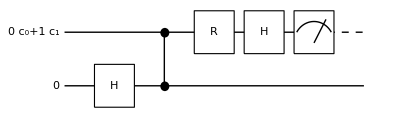

```mathematica
qc=QuissoCircuit[
v0,
S[1,6],
CZ[S[0],S[1]],R0,
S[0,6],Measurement[S[0]]
];
g=Graphics[qc]
```

```mathematica
v=QuissoExpression[qc]
```

(␣ ((c_0+c_1) Cos[α/2]-ⅈ (c_0-c_1) Sin[α/2]))/(√2 √(c_0 c_0^*+c_1 c_1^*))+(1_S_1 ((c_0-c_1) Cos[α/2]-ⅈ (c_0+c_1) Sin[α/2]))/(√2 √(c_0 c_0^*+c_1 c_1^*))

```mathematica
v=v/.rules//Simplify//LogicalForm;
vv=QuissoFactor[v,S[0]]//Simplify
w=vv[[2]]
```

0_S_0⊗((0_S_1 ((c_0+c_1) Cos[α/2]-ⅈ (c_0-c_1) Sin[α/2])+1_S_1 ((c_0-c_1) Cos[α/2]-ⅈ (c_0+c_1) Sin[α/2]))/(√2))

(0_S_1 ((c_0+c_1) Cos[α/2]-ⅈ (c_0-c_1) Sin[α/2])+1_S_1 ((c_0-c_1) Cos[α/2]-ⅈ (c_0+c_1) Sin[α/2]))/(√2)

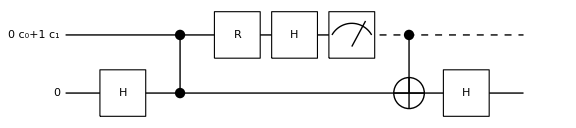

```mathematica
qc=QuissoCircuit[
v0,
S[1,6],
CZ[S[0],S[1]],
R0,S[0,6],
Measurement[S[0]],
CNOT[S[0],S[1]],
S[1,6]
]
```

```mathematica
v1=LogicalForm[QuissoExpression[qc]/.rules,S[{0,1}]]//Simplify
v1=QuissoFactor[v1,S[0]][[2]]
```

c_0 1_S_00_S_1 (Cos[α/2]-ⅈ Sin[α/2])+c_1 1_S_01_S_1 (Cos[α/2]+ⅈ Sin[α/2])

c_0 0_S_1 (Cos[α/2]-ⅈ Sin[α/2])+c_1 1_S_1 (Cos[α/2]+ⅈ Sin[α/2])

```mathematica
v2=Rotation[α,S[1,3]]**ProductState[S[1]->c[{0,1}]]//QuissoExpand;
v2-v1//DefaultForm//Garner
```

0

## Example 2

```mathematica
Quit[]
```

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

```mathematica
Let[Real,α,β,γ]
Let[Complex,c]
```

```mathematica
R1=Rotation[α,S[1,3],Label->"R"];
R2=Rotation[β,S[2,3],Label->Superscript["R",′]];
R3=Rotation[γ,S[3,3],Label->Superscript["R",″]];
```

```mathematica
jj=Range[4]
kk=Range[0,4]
SS=S[kk,None]
```

{1,2,3,4}

{0,1,2,3,4}

{S_0,S_1,S_2,S_3,S_4}

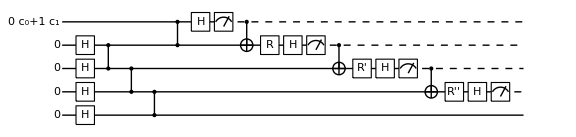

```mathematica
qc=QuissoCircuit[
ProductState[S[0]->{c[0],c[1]},S[{1,2,3,4}]->{1,0}],
S[jj,6],
CZ[S[1],S[2]],CZ[S[2],S[3]],CZ[S[3],S[4]],
CZ[S[0],S[1]],
S[0,6],Measurement[S[0]],
CNOT[S[0],S[1]],R1,
S[1,6],Measurement[S[1]],
CNOT[S[1],S[2]],R2,
S[2,6],Measurement[S[2]],
CNOT[S[2],S[3]],R3,
S[3,6],Measurement[S[3]]
];
g=Graphics[qc,ImageSize->Large]
```

```mathematica
Timing[mat=Matrix[qc];]
expr=QuissoExpression[mat,SS]/.{c[0]Conjugate[c[0]]+c[1]Conjugate[c[1]]->1}
```

{1.43951,Null}

-1_S_01_S_11_S_2 (Cos[α/2] (Cos[β/2] (c_1 Cos[γ/2]+ⅈ c_0 Sin[γ/2])+Sin[β/2] (ⅈ c_1 Cos[γ/2]+c_0 Sin[γ/2]))+Sin[α/2] (Sin[β/2] (c_0 Cos[γ/2]-ⅈ c_1 Sin[γ/2])+Cos[β/2] (-ⅈ c_0 Cos[γ/2]+c_1 Sin[γ/2])))-1/2 1_S_01_S_11_S_21_S_4 (c_0 Cos[1/2 (α-β-γ)]+c_0 Cos[1/2 (α+β-γ)]-c_1 Cos[1/2 (α-β+γ)]+c_1 Cos[1/2 (α+β+γ)]-ⅈ c_1 Sin[1/2 (α-β-γ)]-ⅈ c_1 Sin[1/2 (α+β-γ)]+ⅈ c_0 Sin[1/2 (α-β+γ)]-ⅈ c_0 Sin[1/2 (α+β+γ)])

```mathematica
LogicalForm[expr,SS]//Simplify
```

-1_S_01_S_11_S_20_S_30_S_4 (Cos[α/2] (Cos[β/2] (c_1 Cos[γ/2]+ⅈ c_0 Sin[γ/2])+Sin[β/2] (ⅈ c_1 Cos[γ/2]+c_0 Sin[γ/2]))+Sin[α/2] (Sin[β/2] (c_0 Cos[γ/2]-ⅈ c_1 Sin[γ/2])+Cos[β/2] (-ⅈ c_0 Cos[γ/2]+c_1 Sin[γ/2])))-1/2 1_S_01_S_11_S_20_S_31_S_4 (c_0 Cos[1/2 (α-β-γ)]+c_0 Cos[1/2 (α+β-γ)]-c_1 Cos[1/2 (α-β+γ)]+c_1 Cos[1/2 (α+β+γ)]-ⅈ c_1 Sin[1/2 (α-β-γ)]-ⅈ c_1 Sin[1/2 (α+β-γ)]+ⅈ c_0 Sin[1/2 (α-β+γ)]-ⅈ c_0 Sin[1/2 (α+β+γ)])